### Conventions

The 4-point function of scalar Virasoro primary operators can be parameterized as

	⟨O_1(x_1)O_2(x_2)O_3(x_3)O_4(x_4)⟩=1/(|x_12|^Δ_12|x_34|^Δ_34|x_13|^Δ_13|x_24|^Δ_24|x_14|^Δ_14|x_23|^Δ_23)Σ_O G_O(z)G_O(z̄),
where the sum runs over Virasoro primaries, Δ_ij=Δ_i+Δ_j-1/3(Δ_1+Δ_2+Δ_3+Δ_4) and the conformal cross-ratios are defined by
	z z̄=(x_12^2 x_34^2)/(x_13^2 x_24^2),
	(1-z)(1-z̄)=(x_14^2 x_23^2)/(x_13^2 x_24^2).

In the symmetric case O_3=O_2 and O_4=O_1, we can write

	⟨O_1(x_1)O_2(x_2)O_2(x_3)O_1(x_4)⟩=1/(|x_14|^(2Δ1)|x_23|^(2Δ2))[(1-z)(1-z̄)]^((Δ_1+Δ_2)/3)/[z z̄]^((Δ_1+Δ_2)/6)Σ_O G_O(z)G_O(z̄),

For convenience, we define H(z)=z^((Δ_1+Δ_2+Δ_3+Δ_4)/6)/(1-z)^(Δ_23/2)G(z), in terms of which
	⟨O_1(x_1)O_2(x_2)O_3(x_3)O_4(x_4)⟩=1/(|x_12|^(Δ_1+Δ_2)|x_34|^(Δ_3+Δ_4))((|x_14|)/(|x_24|))^(Δ_2-Δ_1)((|x_14|)/(|x_13|))^(Δ_3-Δ_4)Σ_O H_O(z)H_O(z̄)

For each Virasoro primary operator O, the function H_O(z)H_O(z̄) can be expanded in a sum over quasi-primary operators ψ with dimension Δ and spin j as
	H_O(z)H_O(z̄)=∑λ_(12ψ)λ_(34ψ)G_(Δ,j)(z,z̄)
where
	G_(Δ,0)(z,z̄)=k_Δ(z)k_Δ(z̄)
	G_(Δ,j)(z,z̄)=k_(Δ-j)(z)k_(Δ+j)(z̄)+k_(Δ+j)(z)k_(Δ-j)(z̄)		(j>0)
and
	k_β(z)=z^(β/2) _2 F_1((β-Δ_1+Δ2)/2,(β+Δ_3-Δ_4)/2,β,z)

```mathematica
k[β_,Δ12_,Δ34_][z_]=z^(β/2)Hypergeometric2F1[(β-Δ12)/2,(β+Δ34)/2,β,z];
g[Δ_,l_,Δ12_,Δ34_][z_,zbar_]=1/(1+KroneckerDelta[l,0])(k[Δ+l,Δ12,Δ34][z]k[Δ-l,Δ12,Δ34][zbar]+k[Δ-l,Δ12,Δ34][z]k[Δ+l,Δ12,Δ34][zbar]);
g[Δ_,l_,Δ12_][z_,zbar_]:=g[Δ,l,Δ12,-Δ12][z,zbar]
g[Δ_,l_][z_,zbar_]:=g[Δ,l,0,0][z,zbar]
```

Finally, we will also use the ρ coordinate defined by

```mathematica
ρ=(1-√(1-z))/(1+√(1-z));
```

### Series expansion of the conformal blocks

The conformal blocks admit a series expansion in the form
	G_(Δ,j)(r e^(-i ϕ),r e^(i ϕ))=Σ_(n=0)^∞Σ_(m=-j-n)^(j+n)r^(Δ+n)e^(i ϕ m)c_(n,m)(Δ,j)

```mathematica
gseriescoefficient::outofrange="Error: parameters (n, l, i, j) = (`1`, `2`, `3`, `4`) out of range";
gseriescoefficient::indeterminate="Error: impossible to perform the Taylor expansion of the conformal block";
gseriescoefficient[Δ_,n_,l_,Δ12_][i_,j_]:=Module[{},
If[n<0||l<0||l>n||i<0||j<0||j>i,
Message[gseriescoefficient::outofrange,n,l,i,j];
Return[0]
];
If[Δ==0&&Δ12≠0,
(* if Δ = 0 the intermediate operator is in the identity Virasoro block, so we must have Δ12 = 0 *)
Message[gseriescoefficient::indeterminate];
Return[Null]
];
If[Δ==0&&(l==0||l==n),
If[n==0,
If[i==0,1,0],
If[(j==0||j==i)&&i≥n,Pochhammer[n,i-n]^2/((i-n)!Pochhammer[2n,i-n]),0]
],
If[2l==n,
If[i-j≥l&&j≥l,(Pochhammer[(Δ-Δ12)/2+l,j-l]^2 Pochhammer[(Δ-Δ12)/2+l,i-j-l]^2)/((j-l)!(i-j-l)!Pochhammer[Δ+2l,j-l]Pochhammer[Δ+2l,i-j-l]),0],
If[i-j≥l&&j≥n-l,(Pochhammer[(Δ-Δ12)/2+n-l,j-n+l]^2 Pochhammer[(Δ-Δ12)/2+l,i-j-l]^2)/((j-n+l)!(i-j-l)!Pochhammer[Δ+2n-2l,j-n+l]Pochhammer[Δ+2l,i-j-l]),0]+If[i-j≥n-l&&j≥l,(Pochhammer[(Δ-Δ12)/2+n-l,i-j-n+l]^2 Pochhammer[(Δ-Δ12)/2+l,j-l]^2)/((i-j-n+l)!(j-l)!Pochhammer[Δ+2n-2l,i-j-n+l]Pochhammer[Δ+2l,j-l]),0]
]
]
]
```

Check of the expansion for arbitrary scaling dimension and spin:

```mathematica
Table[Module[{Δ,Δ12,n,l},
Δ=RandomInteger[{0,5}]/RandomInteger[{1,5}];
Δ12=If[Δ==0,0,RandomInteger[{0,5}]/RandomInteger[{1,5}]];
n=RandomInteger[{0,10}];
l=RandomInteger[{0,Floor[n/2]}];
Simplify[Series[ϵ^-Δ g[Δ+n,n-2l,Δ12][ϵ /η,ϵ η],{ϵ,0,8}]-∑_(i=n)^8 ϵ^i∑_(j=0)^i η^(2j-i)gseriescoefficient[Δ,n,l,Δ12][i,j],η>0]//Normal
],{20}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

### QuasiPrimaryData

The  function QuasiPrimaryData computes the scaling dimension, spin and OPE coefficients of all quasi-primary operators entering in the OPE of 2 Virasoro primary operators O_1 and O_2.

Its arguments are:
- Δ_1: the scaling dimension of the Virasoro primary O_1
- Δ_2: the scaling dimension of the Virasoro primary O_2
- Δ: the scaling dimension of the exchanged Virasoro primary O; this can be a list if there are more than one exchanged Virasoro primaries
- H: the Virasoro conformal block; this can also be a list of the same length as the previous argument. This is the function appearing in the expansion
	⟨O_1(x_1)O_2(x_2)O_2(x_3)O_1(x_4)⟩=1/(|x_12 x_34|^(Δ_1+Δ_2))((|x_14^2|)/(|x_13 x_24|))^(Δ_2-Δ_1)Σ_O H_O(z)H_O(z̄)

- Δ_max: the largest scaling dimension up to which the quasi-primary data is extracted; note that if Δ_max is large, the evaluation of the function can take a significant time.

The output is in the form of a list of elements in the form {Δ+n, j, λ^2}, corresponding respectively to the scaling dimension, spin and OPE coefficient squared of all the quasi primary operators in the OPE.

```mathematica
QuasiPrimaryData::failure="Error: unable to expand the Virsoro block in global conformal blocks.";
QuasiPrimaryData[Δ1_,Δ2_,Δ_,H_,Δmax_]:=Module[{nmax,Hseries,Gcoefficients,ϵ,data,n,l,λ,i,j},
If[Head[Δ]===List&&Head[H]===List&&Length[Δ]==Length[H],
Return[CombineOPEData[Table[QuasiPrimaryData[Δ1,Δ2,Δ[[i]],H[[i]],Δmax],{i,Length[Δ]}]]]];
nmax=Floor[Δmax-Δ];
Hseries=Series[ϵ^(-Δ/2)H[ϵ],{ϵ,0,nmax}];
Gcoefficients=Table[SeriesCoefficient[Hseries,j]SeriesCoefficient[Hseries,n-j],{n,0,nmax},{j,0,n/2}];
data={};
For[n=0,n≤nmax,n++,
For[l=0,l≤n/2,l++,
λ=Gcoefficients[[n+1,l+1]];
If[λ≠0,
AppendTo[data,{Δ+n,n-2l,λ}];
For[i=n,i≤nmax,i++,
For[j=0,j≤i/2,j++,
Gcoefficients[[i+1,j+1]]-=λ gseriescoefficient[Δ,n,l,Δ1-Δ2][i,j]
]
]
]
];
];
If[DeleteDuplicates[Flatten[Gcoefficients]]=!={0},Message[QuasiPrimaryData::failure]];
data
]
QuasiPrimaryData[Δ1_,Δ2_,Δ_,H_]:=QuasiPrimaryData[Δ1,Δ2,Δ,H,10]
```

```mathematica
CombineOPEData[data_List]:=Sort[Join@@data,If[#1[[1]]==#2[[1]],#1[[2]]>#2[[2]],#1[[1]]<#2[[1]]]&]
```

Warning: This method of extracting the conformal data does not discriminate between quasi-primary operators with degenerate dimensions and spins. If this occurs, the OPE coefficient that is returned by the method is the sum of the OPE coefficients squared.

```mathematica
SortBySpin[data_List]:=Sort[data,If[#1[[2]]==#2[[2]],#1[[1]]<#2[[1]],#1[[2]]<#2[[2]]]&]
SortByTwist[data_List]:=Sort[data,If[#1[[1]]-#1[[2]]==#2[[1]]-#2[[2]],#1[[1]]<#2[[1]],#1[[1]]-#1[[2]]<#2[[1]]-#2[[2]]]&]
```

```mathematica
ToConformalWeights[data_List]:=Map[{(#[[1]]+#[[2]])/2,(#[[1]]-#[[2]])/2}&,data]
```

## Ising model

The Ising model has 2 Virasoro primaries σ and  ϵ satisfying the OPEs:
	σ×σ~1+ϵ
	σ×ϵ~σ
	ϵ×ϵ~1

Their scaling dimensions are:

```mathematica
Δσ=1/8;
Δϵ=1;
```

The Virasoro conformal blocks can for instance be found in eq. (B.1) of arXiv:1703.00278, where they are expressed in ρ coordinates.
Alternatively, they correspond to the blocks computed in Exercise 12.7 of the Yellow Book (di Francesco, Mathieu & Sénéchal).

### ⟨σσσσ⟩

```mathematica
Hσσ1[z_]=1/(1-z)^(1/8)((1+√(1-z))/2)^(1/2);
Simplify[Hσσ1[z]==1/((1-ρ^2)^(1/4)),z<1]
```

True

```mathematica
Hσσϵ[z_]=1/(1-z)^(1/8)((1-√(1-z))/2)^(1/2);
Simplify[Hσσϵ[z]==(√ρ)/((1-ρ^2)^(1/4)),z<1]
```

True

```mathematica
OPEdataσσ1=QuasiPrimaryData[Δσ,Δσ,0,Hσσ1]
```

{{0,0,1},{2,2,1/64},{4,4,9/40960},{4,0,1/4096},{6,6,25/3670016},{6,2,9/2621440},{8,8,15527/57579405312},{8,4,25/234881024},{8,0,81/1677721600},{10,10,251145/20882130993152},{10,6,15527/3685081939968},{10,2,45/30064771072}}

```mathematica
OPEdataσσϵ=QuasiPrimaryData[Δσ,Δσ,Δϵ,Hσσϵ]
```

{{1,0,1/4},{5,4,1/65536},{7,6,1/1310720},{9,8,1125/30064771072},{9,0,1/1073741824}}

```mathematica
IdentityQuasiPrimaries=OPEdataσσ1[[All,1;;2]]
σσ1OPEcoefficients=OPEdataσσ1[[All,3]]^(1/2);
```

{{0,0},{2,2},{4,4},{4,0},{6,6},{6,2},{8,8},{8,4},{8,0},{10,10},{10,6},{10,2}}

```mathematica
IdentityQuasiPrimaries//SortByTwist//ToConformalWeights
```

{{0,0},{2,0},{4,0},{6,0},{8,0},{10,0},{2,2},{4,2},{6,2},{8,2},{4,4},{6,4}}

```mathematica
ϵQuasiPrimaries=OPEdataσσϵ[[All,1;;2]]
```

{{1,0},{5,4},{7,6},{9,8},{9,0}}

```mathematica
OPEdataσσ=CombineOPEData[{OPEdataσσ1,OPEdataσσϵ}];
OPEdataσσ==QuasiPrimaryData[Δσ,Δσ,{0,Δϵ},{Hσσ1,Hσσϵ}]
```

True

```mathematica
(*SortBySpin[OPEdataσσ]*)
```

```mathematica
(*SortByTwist[OPEdataσσ]*)
```

Each of the following commands takes about 30 seconds to evaluate on my laptop:

```mathematica
(*Length[OPEdataσσ1=QuasiPrimaryData[Δσ,Δσ,0,Hσσ1,100]]//Timing
Length[OPEdataσσϵ=QuasiPrimaryData[Δσ,Δσ,Δϵ,Hσσϵ,100]]//Timing
OPEdataσσ=CombineOPEData[{OPEdataσσ1,OPEdataσσϵ}];*)
```

```mathematica
(*SetDirectory[NotebookDirectory[]];
Export["CFTdata/Ising_ss1.dat",OPEdataσσ1]
Export["CFTdata/Ising_sse.dat",OPEdataσσϵ]
Export["CFTdata/Ising_ss.dat",OPEdataσσ]*)
```

### ⟨ϵϵϵϵ⟩

```mathematica
Hϵϵ[z_]=(1-z+z^2)/(1-z);
Hϵϵ[z]==(1+14 ρ^2+ρ^4)/((1-ρ^2)^2)//Simplify
```

True

```mathematica
Series[Hϵϵ[r],{r,0,20}]//Simplify
```

1+r^2+r^3+r^4+r^5+r^6+r^7+r^8+r^9+r^10+r^11+r^12+r^13+r^14+r^15+r^16+r^17+r^18+r^19+r^20+O[r]^21

```mathematica
(*∑_(n=0)^10 r^n∑_(j=0)^n η^(2j-n)(1-KroneckerDelta[1,j])(1-KroneckerDelta[1,n-j])
%-Series[Hϵϵ[r/η]Hϵϵ[r η],{r,0,10}]*)
```

```mathematica
(*Table[λ[(op[[1]]-op[[2]])/4,op[[2]]/2]=op[[3]],{op,QuasiPrimaryData[Δϵ,Δϵ,0,Hϵϵ,50]}];*)
```

```mathematica
(*G=∑_(t=0)^4 ∑_(l=0)^4 λ[t,l]g[4t+2l,2l][r/η,r η];*)
```

```mathematica
(*G=∑_(t=0)^12 ∑_(l=0)^25 λ[t,l]∑_(n=4t+2l)^8 r^n∑_(j=0)^n η^(2j-n)gseriescoefficient[0,4t+2l,2t,0][n,j];*)
```

```mathematica
(*Series[G,{r,0,8}]
%==Series[Hϵϵ[r/η]Hϵϵ[r η],{r,0,8}]*)
```

```mathematica
(*G=∑_(n=0)^8 ∑_(t=0)^12 ∑_(l=0)^25 λ[t,l] r^(4t+2l+n)∑_(j=0)^(4t+2l+n) η^(2j-(4t+2l+n))gseriescoefficient[0,4t+2l,2t,0][(4t+2l+n),j];*)
```

```mathematica
(*G=∑_(n=0)^8 ∑_(l=0)^25 ∑_(t=0)^(n/4) λ[t,l] r^(n+2l)∑_(j=0)^(n+2l) η^(2j-(n+2l))gseriescoefficient[0,4t+2l,2t,0][(n+2l),j];*)
```

```mathematica
(*G=∑_(n=0)^10 r^n∑_(j=0)^n η^(2j-n)∑_(l=0)^(n/2) ∑_(t=0)^((n-2l)/4) λ[t,l]gseriescoefficient[0,4t+2l,2t,0][n,j]
%-Series[Hϵϵ[r/η]Hϵϵ[r η],{r,0,10}]*)
```

```mathematica
(*Table[λ[t,l]gseriescoefficient[0,4t+2l,2t,0][n,0],{n,0,12},{l,0,n/2},{t,0,n/4-l/2}]
Map[Total[#,2]&,%]*)
```

```mathematica
OPEdataϵϵ=QuasiPrimaryData[Δϵ,Δϵ,0,Hϵϵ]
```

{{0,0,1},{2,2,1},{4,4,1/10},{4,0,1},{6,6,1/126},{6,2,1/10},{8,8,1/1716},{8,4,1/126},{8,0,1/100},{10,10,1/24310},{10,6,1/1716},{10,2,1/1260}}

Verification: the quasi-primaries appearing in this OPE are the same as the ones appearing in the σ×σ OPE (restricted to the identity Virasoro)

```mathematica
OPEdataϵϵ[[All,1;;2]]==IdentityQuasiPrimaries
```

True

```mathematica
ϵϵ1OPEcoefficients=OPEdataϵϵ[[All,3]]^(1/2);
```

The following command takes about 30 seconds to evaluate on my laptop:

```mathematica
(*Length[OPEdataϵϵ=QuasiPrimaryData[Δϵ,Δϵ,0,Hϵϵ,100]]//Timing*)
```

```mathematica
(*SetDirectory[NotebookDirectory[]];
Export["CFTdata/Ising_ee.dat",OPEdataϵϵ]*)
```

The OPE coefficients take a simple analytic form:

```mathematica
λ2[Δ_,l_]:=If[Δ==l,
If[l==0,1,(Gamma[l-1]Gamma[l])/Gamma[2l-2]],
(Gamma[(Δ-l)/2-1]Gamma[(Δ-l)/2]Gamma[(Δ+l)/2-1]Gamma[(Δ+l)/2])/(Gamma[Δ-l-2]Gamma[Δ+l-2])
]
```

```mathematica
Map[λ2[#[[1]],#[[2]]]==#[[3]]&,OPEdataϵϵ]//DeleteDuplicates
```

{True}

```mathematica
(*nop=5;
1/Hϵϵ[z]^2 Accumulate[Table[op[[3]]g[op[[1]],op[[2]]][z,z],{op,OPEdataϵϵ[[1;;nop]]}]]//FullSimplify;
Plot[%,{z,-1,1},PlotStyle->Table[{Blue,Opacity[1-(i-1)/nop]},{i,nop}],PlotRange->{0,1.2}]*)
```

### ⟨σϵϵσ⟩

```mathematica
Hσϵ[z_]=(z^(1/16)(1+z))/(2(1-z));
Simplify[Hσϵ[z]==(ρ^(1/16)(1+6ρ+ρ^2))/(2^(7/8)(1-ρ)^2(1+ρ)^(1/8)),z<1]
```

True

```mathematica
OPEdataσϵ=QuasiPrimaryData[Δσ,Δϵ,Δσ,Hσϵ]
```

{{1/8,0,1/4},{25/8,3,1/102},{41/8,5,1/2090},{49/8,6,1/431730},{49/8,0,1/2601},{57/8,7,225/8822926},{65/8,8,1/4373439},{65/8,2,1/53295},{73/8,9,1039/732571994},{73/8,3,1/11009115}}

```mathematica
σQuasiPrimaries=OPEdataσϵ[[All,1;;2]]
```

{{1/8,0},{25/8,3},{41/8,5},{49/8,6},{49/8,0},{57/8,7},{65/8,8},{65/8,2},{73/8,9},{73/8,3}}

```mathematica
σQuasiPrimaries//SortByTwist//ToConformalWeights
```

{{1/16,1/16},{49/16,1/16},{81/16,1/16},{97/16,1/16},{113/16,1/16},{129/16,1/16},{145/16,1/16},{49/16,49/16},{81/16,49/16},{97/16,49/16}}

The following command takes about 2.5 minutes to evaluate on my laptop:

```mathematica
(*Length[OPEdataσϵ=QuasiPrimaryData[Δσ,Δϵ,Δσ,Hσϵ,100]]//Timing*)
```

```mathematica
(*SetDirectory[NotebookDirectory[]];
Export["CFTdata/Ising_se.dat",OPEdataσϵ]*)
```

### ⟨σσϵϵ⟩

Consistency check: the 4-point function ⟨σσϵϵ⟩ can be expanded in conformal blocks

```mathematica
Hσσϵϵ[z_]=(2-z)/(2 √(1-z));
Hσσϵϵ[z]==(1+ρ^2)/(1-ρ^2)//Simplify
```

True

```mathematica
Series[Hσσϵϵ[ϵ z]Hσσϵϵ[ϵ x]-Sum[σσ1OPEcoefficients[[i]]ϵϵ1OPEcoefficients[[i]](g@@IdentityQuasiPrimaries[[i]])[ϵ z,ϵ x],{i,Length[IdentityQuasiPrimaries]}],{ϵ,0,8}]
```

((175 x^8-√31054 x^8+175 z^8-√31054 z^8) ϵ^8)/14057472+O[ϵ]^9

Starting at dimension 8, there are actually quasi-primary operators that are degenerate in scaling dimension and spin. We can correct the list “by hand”, and we find:

```mathematica
CorrectedIdentityQuasiPrimaries={{0,0},{2,2},{4,4},{4,0},{6,6},{6,2},{8,8},{8,8},{8,4},{8,0},{10,10},{10,10},{10,6},{10,6},{10,2}};
Correctedϵϵ1OPEcoefficients={1,1,1/(√10),1,1/(3 √14),1/(√10),0,1/(2 √429),1/(3 √14),1/10,0, 1/(√24310),0,1/(2 √429),1/(6 √35)};
Correctedσσ1OPEcoefficients={1,1/8,3/(64 √10),1/64,5/(512 √14),3/(512 √10),1/16384,175/(16384 √429),5/(4096 √14),9/40960,15/(131072 √34),(441 √5)/(131072 √4862),1/131072,175/(131072 √429),(3 √5)/(65536 √7)};
```

```mathematica
Series[Hσσ1[ϵ z]Hσσ1[ϵ x]-Sum[Correctedσσ1OPEcoefficients[[i]]^2(g@@CorrectedIdentityQuasiPrimaries[[i]])[ϵ z,ϵ x],{i,Length[CorrectedIdentityQuasiPrimaries]}],{ϵ,0,10}]
Series[Hϵϵ[ϵ z]Hϵϵ[ϵ x]-Sum[Correctedϵϵ1OPEcoefficients[[i]]^2(g@@CorrectedIdentityQuasiPrimaries[[i]])[ϵ z,ϵ x],{i,Length[CorrectedIdentityQuasiPrimaries]}],{ϵ,0,10}]
Series[Hσσϵϵ[ϵ z]Hσσϵϵ[ϵ x]-Sum[Correctedσσ1OPEcoefficients[[i]]Correctedϵϵ1OPEcoefficients[[i]](g@@CorrectedIdentityQuasiPrimaries[[i]])[ϵ z,ϵ x],{i,Length[CorrectedIdentityQuasiPrimaries]}],{ϵ,0,10}]
```

O[ϵ]^11

O[ϵ]^11

O[ϵ]^11

## Free scalar theory (connected part of the correlation function)

Consider the operator O=T T̄, where T=(∂ϕ)^2 and T̄=(OverBar[∂]ϕ)^2:

```mathematica
HTTbar[z_]=(z^2(1-z+z^2))/(1-z)^2;
```

```mathematica
Series[HTTbar[ϵ z]HTTbar[ϵ x]-(g[4,0][ϵ z,ϵ x]+11/10 g[6,2][ϵ z,ϵ x]+29/126 g[8,4][ϵ z,ϵ x]+121/100 g[8,0][ϵ z,ϵ x]+5/156 g[10,6][ϵ z,ϵ x]+319/1260 g[10,2][ϵ z,ϵ x]+89/24310 g[12,8][ϵ z,ϵ x]+11/312 g[12,4][ϵ z,ϵ x]+841/15876 g[12,0][ϵ z,ϵ x]),{ϵ,0,12}]
```

O[ϵ]^13

```mathematica
OPEdataTTbar=QuasiPrimaryData[4,4,4,HTTbar,12]
```

{{4,0,1},{6,2,11/10},{8,4,29/126},{8,0,121/100},{10,6,5/156},{10,2,319/1260},{12,8,89/24310},{12,4,11/312},{12,0,841/15876}}

The following command takes about 30 seconds to evaluate on my laptop:

```mathematica
(*Length[OPEdataTTbar=QuasiPrimaryData[4,4,4,HTTbar,100]]//Timing*)
```

```mathematica
(*SetDirectory[NotebookDirectory[]];
Export["CFTdata/FreeScalar_TTbar.dat",OPEdataTTbar]*)
```

## Tests of OPE convergence

```mathematica
ConvergencePlot[z_,zbar_,Δ1_,Δ2_,H_,OPEdata_,plotstyle_]:=Module[{points},
points=H[z]H[zbar]-Accumulate[Map[#[[3]]g[#[[1]],#[[2]],Δ1-Δ2,Δ2-Δ1][z,zbar]&,OPEdata]];
ListLogPlot[points,PlotRange->{{0,Length[points]},{10^(-$MachinePrecision),2First[points]}},AxesLabel->{"# of operators","error"},ImageSize->600,PlotStyle->plotstyle]
]
ConvergencePlot[z_,zbar_,Δ1_,Δ2_,G_,OPEdata_]:=ConvergencePlot[z,zbar,Δ1,Δ2,G,OPEdata,Automatic]
```

```mathematica
SetDirectory[NotebookDirectory[]];
OPEdataσσ1=ToExpression[Import["CFTdata/Ising_ss1.dat"]];
OPEdataσσϵ=ToExpression[Import["CFTdata/Ising_sse.dat"]];
OPEdataσσ=ToExpression[Import["CFTdata/Ising_ss.dat"]];
OPEdataϵϵ=ToExpression[Import["CFTdata/Ising_ee.dat"]];
OPEdataσϵ=ToExpression[Import["CFTdata/Ising_se.dat"]];
```

Comparison of the convergence of the the identity Virasoro operators (red) and the ϵ Virasoro operators (blue) in the σ×σ OPE:

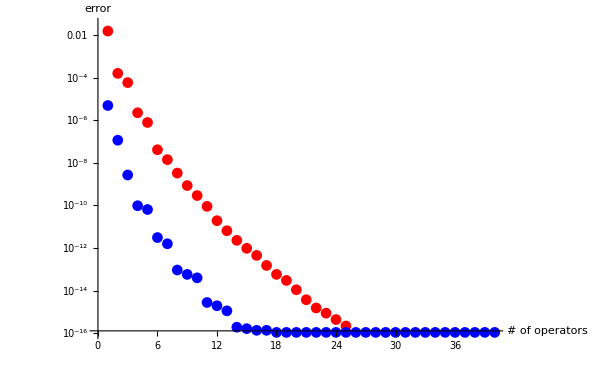

```mathematica
Show[ConvergencePlot[0.5,0.5,Δσ,Δσ,Hσσ1,OPEdataσσ1[[1;;40]],Red],ConvergencePlot[0.5,0.5,Δσ,Δσ,Hσσϵ,OPEdataσσϵ[[1;;40]],Blue]]
```

Convergence of the ϵ×ϵ OPE:

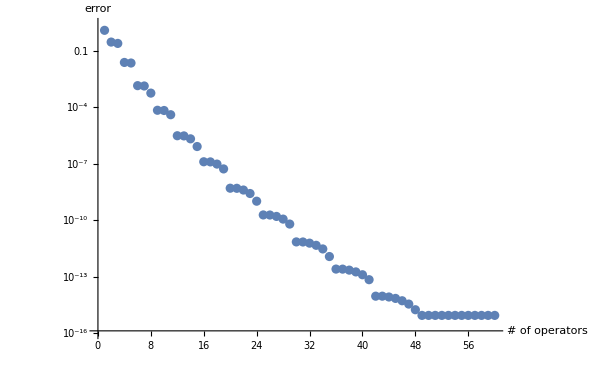

```mathematica
ConvergencePlot[0.5,0.5,Δϵ,Δϵ,Hϵϵ,OPEdataϵϵ[[1;;60]]]
```

Convergence of the σ×ϵ OPE:

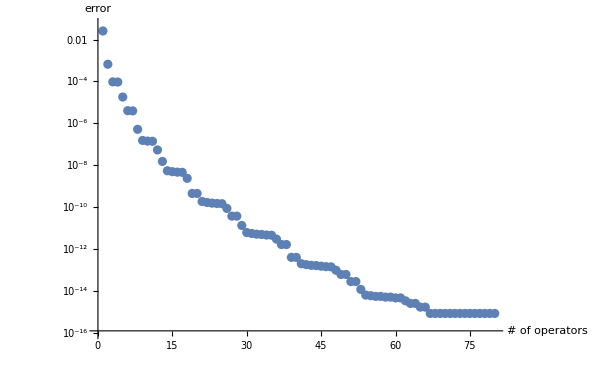

```mathematica
ConvergencePlot[0.5,0.5,Δσ,Δϵ,Hσϵ,OPEdataσϵ[[1;;80]]]
```

## Evaluation timing

```mathematica
(*timingdata=Table[{nmax,First[Timing[QuasiPrimaryData[Δσ,Δσ,0,Hσσ1,nmax]]]},{nmax,{10,15,20,25,30,35,40,45,50,60,70,80,100}}]*)
```

```mathematica
(*Select[timingdata,First[#]>50&];
timingfit[n_]=Exp[Fit[Log[%],{1,Log[n]},Log[n]]]*)
```

```mathematica
(*Show[ListLogLogPlot[timingdata,PlotStyle->Red],LogLogPlot[timingfit[n],{n,1,100},PlotStyle->{Gray,Dashed}]]*)
```

```mathematica
(*timingfit[200]/60.*)
```

```mathematica
(*timingfit[500]/3600.*)
```